# Asymmetric Frame

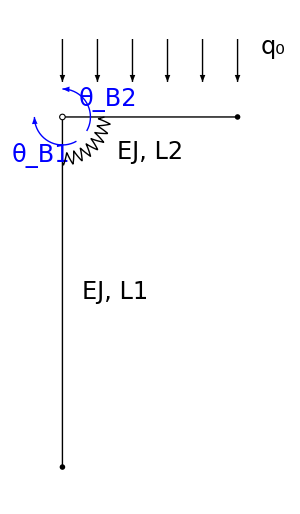

```mathematica
L=1;
EJ=1;
L1=L;
L2=L/2;
EJ1=EJ;
EJ2=EJ;
q0F=150;

α=90°;

pA={0,0};
pB={L1*Cos[α],L1*Sin[α]};
pC={L1*Cos[α]+L2,L1*Sin[α]};

myCircle[o_,r_,{a_,b_},res_]:=Arrow@Table[{Cos[k],Sin[k]}*r+o,{k,a,b,(b-a)/res}];
myCircleSpring[o_,r_,{a_,b_},Δ_,δ_,res_]:=Line@Table[{Cos[k],Sin[k]}*r*(1+Δ*TriangleWave[1.*k*δ])+o,{k,a,b,(b-a)/res}];

cer={Disk[{0,0},0.06],Gray,Triangle[{{-0.5,-0.5},{0,0},{0.5,-0.5}}]};
cerint={EdgeForm[Thick],FaceForm[White],Disk[{0,0},0.06]};
app={Disk[{0,0},0.06],Gray,Triangle[{{-0.5,-0.5},{0,0},{0.5,-0.5}}],Disk[{-0.25,-0.5},0.1],Disk[{0.25,-0.5},0.1]};
inc={Disk[{0,0},0.06],Thickness[0.06],Line[{{0,0},{0,-0.1}}],Gray,Rectangle[{-0.5,-0.6},{0.5,-0.1}]};
pat={Disk[{0,0},0.05],Thickness[0.04],Line[{{-0.5,0.1},{-0.4,0},{0.4,0},{0.5,0.1}}],Gray,Rectangle[{-0.5,-0.6},{0.5,-0.1}]};

g=Graphics[{FilledCurve[{BSplineCurve[{{-0.369,0.},{-0.379,0.386},{-0.430,0.882}}],BSplineCurve[{{-0.430,0.882},{-0.289,0.236},{0,0}}],BSplineCurve[{{0,0},{-0.289,-0.236},{-0.430,-0.882}}],BSplineCurve[{{-0.430,-0.882},{-0.379,-0.386},{-0.369,0.}}]}]}];

myCircle[o_,r_,{a_,b_},res_]:=Arrow@Table[{Cos[k],Sin[k]}*r+o,{k,a,b,(b-a)/res}];

o1={0,0};
θ1=Pi/2;
m1=RotationMatrix[θ1];

o2={0,L1};
θ2=0;
m2=RotationMatrix[θ2];

undef0=Show[
{
ParametricPlot[AffineTransform[{m1,o1}][{x,0}],{x,0,L1},PlotStyle->Directive[Black,Thick]],
ParametricPlot[AffineTransform[{m2,o2}][{x,0}],{x,0,L2},PlotStyle->Directive[Black,Thick]],
Graphics[{Inset[Graphics@inc,{0,0},{0,0},Scaled[0.12]]}],
Graphics[{Inset[Graphics@inc,pC,{0,0},Scaled[0.12],{0,1}]}],
Graphics[{Inset[Graphics@cerint,pB,{0,0},Scaled[0.06]]}],
Graphics[{Black,myCircleSpring[pB,0.12,{-Pi/2,0},0.15,5,200]}],
Table[Graphics[{Arrowheads[{{0.03,1,g}}],Arrow[{{i,(1.1+0.15*q0F/q0F)*L1},{i,1.1*L1}}]}],{i,0,L2,0.2*L2}],
Graphics[Text[Style[Subscript[q, 0],24],{1.2*L2,1.2*L1}]],
Graphics[{Blue,Arrowheads[0.03],myCircle[pB,0.08,{-Pi/3,-Pi},20]}],
Graphics[Text[Style[Subscript[θ, B1],24,Blue],pB+{-0.06,-0.11}]],
Graphics[{Blue,Arrowheads[0.03],myCircle[pB,0.08,{-Pi/6,Pi/2},20]}],
Graphics[Text[Style[Subscript[θ, B2],24,Blue],pB+{0.13,0.05}]],
Graphics[Text[Style["EJ, L1",24,Italic],{0,0.5*L1}+{0.15,0}]],
Graphics[Text[Style["EJ, L2",24,Italic],{0.5*L2,L1}+{0,-0.1}]]
},
PlotRange->{{-0.2*L2,1.2*L2},{0.*L1,1.2*L1}},
AspectRatio->Automatic,
Axes->False,
ImageSize->300
];

Clear[L1,L2,EJ1,EJ2,q0];

Show[undef0]
```

```mathematica
ClearAll["Global`*"];

l1 = l;
l2 = l/2;
EJ1 = EJ;
EJ2 = EJ;
K = β*EJ1/l1;
q0 = λ*EJ1/l1^3;
```

## Elastic solution

```mathematica
v1[s1_] = c1 +c2*s1+c3*s1^2+c4*s1^3;
v2[s2_] = c5+c6*s2+c7*s2^2+c8*s2^3+q0/(24*EJ2)*s2^4;

lininc = {c1,c2,c3,c4,c5,c6,c7,c8,N1,N2};

lineq = {
v1[0]==0,
v1'[0]==0, 
v2[l2]==0, 
v2'[l2]==0, 
-v1'''[l1]==-EJ2/EJ1*α2^2,
-v2'''[0]==EJ1/EJ2*α1^2,
 -v1''[l1]==-K/EJ1*(v2'[0]-v1'[l1]),
-v2''[0]==-K/EJ2*(v2'[0]-v1'[l1]),
v1[l1]==0,
v2[0]==0
};
TableForm[lineq]
```

c1==0
c2==0
c5+(c6 l)/2+(c7 l^2)/4+(c8 l^3)/8+(l λ)/384==0
c6+c7 l+(3 c8 l^2)/4+λ/48==0
-6 c4==-α2^2
-6 c8==α1^2
-2 c3-6 c4 l==-((-c2+c6-2 c3 l-3 c4 l^2) β)/l
-2 c7==-((-c2+c6-2 c3 l-3 c4 l^2) β)/l
c1+c2 l+c3 l^2+c4 l^3==0
c5==0

```mathematica
linsol = Solve[
lineq/.{α1->Sqrt[N1/EJ1], α2->Sqrt[N2/EJ2]}, lininc][[1]]
```

{c1→0,c2→0,c3→-(β λ)/(192 l (8+3 β)),c4→(β λ)/(192 l^2 (8+3 β)),c5→0,c6→((4+β) λ)/(192 (8+3 β)),c7→(β λ)/(96 l (8+3 β)),c8→-((12+5 β) λ)/(48 l^2 (8+3 β)),N1→(EJ (12+5 β) λ)/(8 l^2 (8+3 β)),N2→(EJ β λ)/(32 l^2 (8+3 β))}

```mathematica
N1lin[λ_] = N1/.linsol
N2lin[λ_] = N2/.linsol

θB1lin[λ_] = v1'[l1]/.linsol
θB2lin[λ_] = v2'[0]/.linsol

v1lin[s1_, λ_] = v1[s1]/.linsol
v2lin[s2_, λ_] = v2[s2]/.linsol

{α1lin, α2lin} = {Sqrt[N1lin[λ]/EJ1], Sqrt[N2lin[λ]/EJ2]}
```

(EJ (12+5 β) λ)/(8 l^2 (8+3 β))

(EJ β λ)/(32 l^2 (8+3 β))

(β λ)/(192 (8+3 β))

((4+β) λ)/(192 (8+3 β))

-(s1^2 β λ)/(192 l (8+3 β))+(s1^3 β λ)/(192 l^2 (8+3 β))

(s2^4 λ)/(24 l^3)+(s2^2 β λ)/(96 l (8+3 β))+(s2 (4+β) λ)/(192 (8+3 β))-(s2^3 (12+5 β) λ)/(48 l^2 (8+3 β))

{(√(((12+5 β) λ)/(l^2 (8+3 β))))/(2 √2),(√((β λ)/(l^2 (8+3 β))))/(4 √2)}

## Plot

```mathematica
ClearAll[l, EJ, λ, def, undef, frame, gr, comb, tab]

l =1;
EJ=1;
β=1;
λfin = 150;

undef = Show[
{
ParametricPlot[{0, s1}, {s1, 0, l1}, PlotStyle->Directive[Gray]],
ParametricPlot[{s2, l1}, {s2, 0, l2},PlotStyle->Directive[Gray]]
},
PlotRange->Full
];

def[λ_] := Show[
{
ParametricPlot[{v1lin[s1, λ], s1}, {s1, 0, l1}],
ParametricPlot[{s2, l1-v2lin[s2, λ]}, {s2, 0, l2}]
},
PlotRange->Full
];

frame[λ_]:= Show[{undef, def[λ]}, ImageSize->200];

gr[λ_]:=Show[{
ParametricPlot[{θB1lin[q], q}, {q, 0, λfin},
PlotStyle->Directive[Red],
AspectRatio->1/GoldenRatio,
PlotRangePadding->None,
PlotRangeClipping->True,
PlotLegends->Placed[{Style["θ_B1",14]},{Scaled[{0.35,0.60}], {-1, 1}}]
],
ParametricPlot[{θB2lin[q], q}, {q, 0, λfin},
PlotStyle->Directive[Blue],
AspectRatio->1/GoldenRatio,
PlotRangePadding->None,
PlotRangeClipping->True,
PlotLegends->Placed[{Style["θ_B2",14]},{Scaled[{0.35,0.60}], {-1, 1}}]
],
Graphics[{PointSize[Large],Red,Point[{θB1lin[λ],λ}]}],
Graphics[{PointSize[Large],Blue,Point[{θB2lin[λ],λ}]}]
},
PlotLegends->{{"θ_B1"}, {"θ_B2"}},
FrameLabel->{"θ_B", "q_0/EJ_1"},
PlotRange->Automatic,
Axes->False, 
Frame->True, 
ImageSize->350,
LabelStyle->14
];

comb[λ_]:= Grid[{{frame[λ], gr[λ]}}, Spacings->0];

tab = Table[comb[λ], {λ, 0., λfin, .5}];
ListAnimate[
tab, 
AnimationRunning->False,
AnimationRepetitions->Infinity, 
DefaultDuration->5
]
```

## II order analysis

```mathematica
ClearAll[v1, v2, c1, c2, c3,c4, c5, c6, c7, c8, α1, α2, β, K, EJ, l, q0]

l1 = l;
l2 = l/2;
EJ1 = EJ;
EJ2 = EJ;
K = β*EJ1/l1;
q0 = λ*EJ1/l1^3;

EJ = 1;
l=1;
β=1;
```

## Linear axial forces

```mathematica
v1[s1_] = c1+c2*s1+c3*Cos[α1*s1]+c4*Sin[α1*s1];
v2[s2_] = c5+c6*s2+c7*Cos[α2*s2]+c8*Sin[α2*s2] + q0/(2*α2^2*EJ2)*s2^2;

nleq = {
v1[0]==0, 
v1'[0]==0, 
v2[l2]==0, 
v2'[l2]==0, 
(*-v1'''[l1]-α1^2*v1'[l1]+EJ2/EJ1*α2^2==0, 
-v2'''[0]-α2*v2'[0]-EJ1/EJ2*α1^2==0,*) 
-v1''[l1]==-K/EJ1*(v2'[0]-v1'[l1]), 
-v2''[0]==-K/EJ2*(v2'[0]-v1'[l1]), 
v1[l1]==0, 
v2[0]==0
};

nlinc = {c1,c2,c3,c4,c5,c6,c7,c8};

{RR, MM} = CoefficientArrays[
nleq/.{α1->α1lin, α2->α2lin}, nlinc
]//Normal;
RR = -RR;
MatrixForm[MM]
MatrixForm[RR]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1/2 √(17/22) √λ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1/2 | Cos[(√λ)/(8 √22)] | Sin[(√λ)/(8 √22)]
0 | 0 | 0 | 0 | 0 | 1 | -(√λ Sin[(√λ)/(8 √22)])/(4 √22) | (√λ Cos[(√λ)/(8 √22)])/(4 √22)
0 | -1 | 17/88 λ Cos[1/2 √(17/22) √λ]+1/2 √(17/22) √λ Sin[1/2 √(17/22) √λ] | -1/2 √(17/22) √λ Cos[1/2 √(17/22) √λ]+17/88 λ Sin[1/2 √(17/22) √λ] | 0 | 1 | 0 | (√λ)/(4 √22)
0 | -1 | 1/2 √(17/22) √λ Sin[1/2 √(17/22) √λ] | -1/2 √(17/22) √λ Cos[1/2 √(17/22) √λ] | 0 | 1 | λ/352 | (√λ)/(4 √22)
1 | 1 | Cos[1/2 √(17/22) √λ] | Sin[1/2 √(17/22) √λ] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0)

(0
0
-44
-176
0
352
0
0)

```mathematica
detMM[λ_] = Det[MM]//Simplify
```

1/10903552 λ^(3/2) (-176 (Cos[(√λ)/(8 √22)] (√17 √λ+272 √22 Sin[1/2 √(17/22) √λ])-8 √374 Sin[(√λ)/(8 √22)]+Sin[1/2 √(17/22) √λ] (-272 √22+17 √λ Sin[(√λ)/(8 √22)]))+√17 Cos[1/2 √(17/22) √λ] (√λ (24112+17 λ) Cos[(√λ)/(8 √22)]-4 (5984 √λ+√22 (352+17 λ) Sin[(√λ)/(8 √22)])))

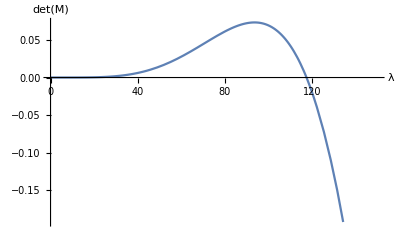

```mathematica
EJ = 1;
l=1;
β=1;

Plot[detMM[λ], {λ, 0, 150}, AxesLabel->{"λ", "det(M)"}]
```

```mathematica
λcr = λ/.FindRoot[detMM[λ]==0, {λ, 120}]
```

117.454

```mathematica
nlsol1 = Solve[
nleq/.{α1->α1lin, α2->α2lin}, nlinc
][[1]];

v1nl[s1_, λ_] = v1[s1]/.nlsol1/.{α1->α1lin, α2->α2lin}//Simplify;
v2nl[s2_, λ_] = v2[s2]/.nlsol1/.{α1->α1lin, α2->α2lin}//Simplify;

θB1nl[λ_] = v1'[l1]/.nlsol1/.{α1->α1lin, α2->α2lin}//Simplify;
θB2nl[λ_] = v2'[0]/.nlsol1/.{α1->α1lin, α2->α2lin}//Simplify;
```

```mathematica
MMcr = MM/.λ->λcr;
MatrixForm[MMcr]
RRcr = RR/.λ->λcr;
MatrixForm[RRcr]

MMCcr = Transpose[Append[Transpose[MMcr],RRcr]];
MatrixForm[MMCcr]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 4.76339 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1/2 | 0.95858 | 0.284824
0 | 0 | 0 | 0 | 0 | 1 | -0.164528 | 0.55372
0 | -1 | -3.60046 | -22.9032 | 0 | 1 | 0 | 0.577646
0 | -1 | -4.7572 | -0.242838 | 0 | 1 | 0.333675 | 0.577646
1 | 1 | 0.0509802 | -0.9987 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0)

(0
0
-44
-176
0
352
0
0)

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 4.76339 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1/2 | 0.95858 | 0.284824 | -44
0 | 0 | 0 | 0 | 0 | 1 | -0.164528 | 0.55372 | -176
0 | -1 | -3.60046 | -22.9032 | 0 | 1 | 0 | 0.577646 | 0
0 | -1 | -4.7572 | -0.242838 | 0 | 1 | 0.333675 | 0.577646 | 352
1 | 1 | 0.0509802 | -0.9987 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0)

```mathematica
MatrixRank[MMcr]
MatrixRank[MMCcr]
```

7

8

### Plot

```mathematica
ClearAll[l, EJ, λ, def, undef, frame, gr, comb, tab]

l =1;
EJ=1;
β=1;
λfin = 150;

undef = Show[
{
ParametricPlot[{0, s1}, {s1, 0, l1}, PlotStyle->Directive[Gray]],
ParametricPlot[{s2, l1}, {s2, 0, l2},PlotStyle->Directive[Gray]]
},
PlotRange->Full
];

def[λ_] := Show[
{
ParametricPlot[{v1lin[s1, λ], s1}, {s1, 0, l1}, PlotStyle->Directive[Black, Dashed]],
ParametricPlot[{s2, l1-v2lin[s2, λ]}, {s2, 0, l2}, PlotStyle->Directive[Black, Dashed]],
ParametricPlot[{v1nl[s1, λ], s1}, {s1, 0, l1}, PlotStyle->Directive[Blue]],
ParametricPlot[{s2, l1-v2nl[s2, λ]}, {s2, 0, l2}, PlotStyle->Directive[Blue]]
},
PlotRange->Full
];

frame[λ_]:= Show[{undef, def[λ]}, ImageSize->200];

gr[λ_]:=Show[{
ParametricPlot[{θB2lin[q], q}, {q, 0, λfin},
PlotStyle->Directive[Black, Dashed],
AspectRatio->1/GoldenRatio,
PlotRangePadding->None,
PlotRangeClipping->True,
PlotLegends->Placed[{Style["θ_B2 linear",14]},{Scaled[{0.35,0.60}], {-1, .5}}]
],
ParametricPlot[{θB2nl[q], q}, {q, 0, λfin},
PlotStyle->Directive[Blue],
AspectRatio->1/GoldenRatio,
PlotRangePadding->None,
PlotRangeClipping->True,
PlotLegends->Placed[{Style["θ_B2 II order",14]},{Scaled[{0.35,0.60}], {-1, .5}}]
],
Graphics[{PointSize[Large],Black,Point[{θB2lin[λ],λ}]}],
Graphics[{PointSize[Large],Red,Point[{θB2nl[λ],λ}]}]
},
FrameLabel->{"θ_B", "q_0/EJ_1"},
PlotRange->Automatic,
Axes->False, 
Frame->True, 
ImageSize->500,
LabelStyle->14
];

comb[λ_]:= Grid[{{frame[λ], gr[λ]}}, Spacings->0];

tab = Table[comb[λ], {λ, 1, λfin, 10}];
ListAnimate[
tab, 
AnimationRunning->False,
AnimationRepetitions->Infinity, 
DefaultDuration->5
]
```

## Non-linear axial forces

```mathematica
ClearAll[v1, v2, c1, c2, c3,c4, c5, c6, c7, c8, α1, α2, β, K, EJ, l, q0, nleq2]

v1[s1_] = c1+c2*s1+c3*Cos[α1*s1]+c4*Sin[α1*s1];
v2[s2_] = c5+c6*s2+c7*Cos[α2*s2]+c8*Sin[α2*s2] + q0/(2*α2^2*EJ2)*s2^2;

l1 = l;
l2 = l/2;
EJ1 = EJ;
EJ2 = EJ;
K = β*EJ1/l1;
q0 = λ*EJ1/l1^3;

EJ = 1;
l=1;
β=1;

linsol2 = Solve[
{
v1[0]==v1nl[0, dλ], 
v1'[0]==Derivative[1, 0][v1nl][0,dλ], 
v1[l1]==v1nl[l1, dλ],
v1'[l1]==Derivative[1, 0][v1nl][l1,dλ],
v2[0]==v2nl[0, dλ], 
v2'[0]==Derivative[1, 0][v2nl][0,dλ], 
v2[l2]==v2nl[l2, dλ],
v2'[l2]==Derivative[1, 0][v2nl][l2,dλ]
},
{c1,c2,c3,c4,c5,c6,c7,c8}
][[1]];

nleq2[λ_] = {
v1[0]==0, 
v1'[0]==0, 
v2[l2]==0, 
v2'[l2]==0, 
-v1'''[l1]-α1^2*v1'[l1]+EJ2/EJ1*α2^2==0, 
-v2'''[0]-α2*v2'[0]-EJ1/EJ2*α1^2==0,
-v1''[l1]==-K/EJ1*(v2'[0]-v1'[l1]), 
-v2''[0]==-K/EJ2*(v2'[0]-v1'[l1]), 
v1[l1]==0, 
v2[0]==0
};

nlinc2 = {c1,c2,c3,c4,c5,c6,c7,c8,α1, α2};

F =  {
v1[0], 
v1'[0], 
v2[l2], 
v2'[l2], 
-v1'''[l1]-α1^2*v1'[l1]+EJ2/EJ1*α2^2, 
-v2'''[0]-α2*v2'[0]-EJ1/EJ2*α1^2,
-v1''[l1]+K/EJ1*(v2'[0]-v1'[l1]), 
-v2''[0]+K/EJ2*(v2'[0]-v1'[l1]), 
v1[l1], 
v2[0]
};

J =Grad[F, nlinc2];
MatrixForm[J]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | α1 | 0 | 0 | 0 | 0 | c4 | 0
0 | 0 | 0 | 0 | 1 | 1/2 | Cos[α2/2] | Sin[α2/2] | 0 | -λ/(4 α2^3)+1/2 c8 Cos[α2/2]-1/2 c7 Sin[α2/2]
0 | 0 | 0 | 0 | 0 | 1 | -α2 Sin[α2/2] | α2 Cos[α2/2] | 0 | -λ/α2^3+c8 Cos[α2/2]-1/2 c7 α2 Cos[α2/2]-c7 Sin[α2/2]-1/2 c8 α2 Sin[α2/2]
0 | -α1^2 | 0 | 0 | 0 | 0 | 0 | 0 | 3 c4 α1^2 Cos[α1]-c3 α1^3 Cos[α1]-3 c3 α1^2 Sin[α1]-c4 α1^3 Sin[α1]-2 α1 (c2+c4 α1 Cos[α1]-c3 α1 Sin[α1])-α1^2 (c4 Cos[α1]-c3 α1 Cos[α1]-c3 Sin[α1]-c4 α1 Sin[α1]) | 2 α2
0 | 0 | 0 | 0 | 0 | -α2 | 0 | -α2^2+α2^3 | -2 α1 | -c6-2 c8 α2+3 c8 α2^2
0 | -1 | α1^2 Cos[α1]+α1 Sin[α1] | -α1 Cos[α1]+α1^2 Sin[α1] | 0 | 1 | 0 | α2 | -c4 Cos[α1]+3 c3 α1 Cos[α1]+c4 α1^2 Cos[α1]+c3 Sin[α1]+3 c4 α1 Sin[α1]-c3 α1^2 Sin[α1] | c8
0 | -1 | α1 Sin[α1] | -α1 Cos[α1] | 0 | 1 | α2^2 | α2 | -c4 Cos[α1]+c3 α1 Cos[α1]+c3 Sin[α1]+c4 α1 Sin[α1] | c8+2 c7 α2+(2 λ)/α2^3
1 | 1 | Cos[α1] | Sin[α1] | 0 | 0 | 0 | 0 | c4 Cos[α1]-c3 Sin[α1] | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0)

```mathematica
detJ = Det[J]
```

1/(8 α2^9)
 |  |  |  |

### Soluzione con il metodo iterativo di Newton

```mathematica
ClearAll[maxiter, l, EJ, q0, α1, α2, α1sq, α2sq, iternum, dλ, λiter,sol2,sol3, λfin, rule, nlincinit];

{α1sq, α2sq} = {α1^2, α2^2};

maxiter = 10^5;

l=1;
EJ=1;
β=1;

λfin = 150;
iternum = 1000;

dλ = λfin/iternum;
λiter=0;

sol2 = nlinc2/.linsol2/.{α1->Sqrt[N1lin[dλ]/EJ1], α2->Sqrt[N2lin[dλ]/EJ2], λ->dλ}//N

nlincinit={c1i, c2i, c3i, c4i, c5i, c6i, c7i,c8i,α1i, α2i};

sol3 = 0*nlinc2;
resθB1={{0,0}};
resθB2 = {{0,0}};
resdetJ={{0,0}};
resN1={{0,0}};
resN2={{0,0}};

Monitor[
For[
i=1, i<iternum+1, i++,

nlincinit=sol2;

λiter = λiter+dλ;

rule = 
FindRoot[
nleq2[λiter], Table[{nlinc2[[j]],nlincinit[[j]]}, {j, 1, Length[nlinc2]}],
MaxIterations->maxiter, 
WorkingPrecision->80];

sol2 = Table[nlinc2[[j]]->rule[[j]], {j , 1, Length[rule]}];

θB1 = v1'[l1]/.Table[nlinc2[[j]]->sol2[[j]], {j , 1, Length[sol2]}]/.λ->λiter//N;
θB2 = v2'[0]/.Table[nlinc2[[j]]->sol2[[j]], {j , 1, Length[sol2]}]/.λ->λiter//N;

detJsol = detJ/.Table[nlinc2[[j]]->sol2[[j]], {j, 1, Length[sol2]}]/.λ->λiter//N;

sol3 = AppendTo[sol3, sol2];

resθB1 = AppendTo[resθB1, {θB1, λiter//N}];
resθB2 = AppendTo[resθB2, {θB2, λiter//N}];
resdetJ = AppendTo[resdetJ, {λiter//N, detJsol}];
resN1 = AppendTo[resN1, {λiter//N, sol2[[Position[nlinc2, α1][[1,1]]]]^2*EJ1}];
resN2 = AppendTo[resN2, {λiter//N, sol2[[Position[nlinc2, α2][[1,1]]]]^2*EJ2}];

Pause[1];
];
Grid[{{"iter = ",i},{"λ = ",λiter//N},{"det(J) = ",detJsol}},Alignment->"."],
Grid[{{ProgressIndicator[i,{1,iternum}]},{"iter = ",i},{"λ = ",λiter//N},{"det(J) = ",detJsol}},Alignment->"."]
]
```

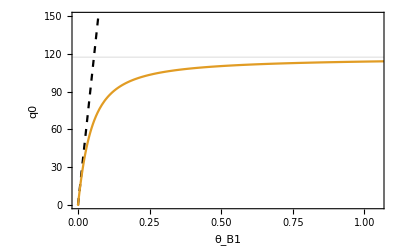

```mathematica
grteB1=Show[{
ParametricPlot[{{θB1lin[λiter],λiter},{θB1nl[λiter],λiter}},{λiter,0,λfin},
PlotRange->{{0,60°},{0,150}},
PlotStyle->{Directive[Black,Dashed],Automatic},
AspectRatio->1/GoldenRatio,
Frame->True,
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameLabel->{"θ_B1","q0"},
LabelStyle->18,
PlotRangePadding->None,
PlotRangeClipping->True,
GridLines->{None,{λcr}}],
ListPlot[resθB1,Joined->True,PlotStyle->Directive[Red]]
}]
```